-Graphics3D-

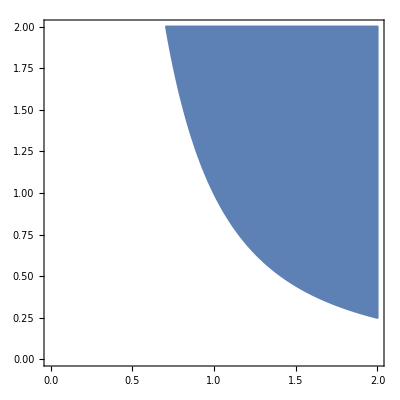

```mathematica
eps = 0.0001;
f1[x_,y_,z_]:= z- x^2/y;
f2[x_,y_]:= y - 1 / x^2;
plt1 = RegionPlot3D[f1[x,y,z]<0,{x,eps,2},{y,eps,2},{z,eps,2}, PlotStyle->"Red"];
plt2 = RegionPlot[f2[x,y]>0,{x,eps,2},{y,eps,2}, PlotStyle->"Red"];
plt1
plt2
```